# Laborator nr.2 la Paradgme de Programare

## Realizarea unui proiect de cercetare în sistemul Mathematica și limbajul Wolfram

Autor: Curmanschii Anton, MIA2201

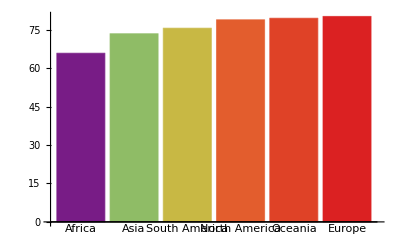

```mathematica
data=(
CountryData[]
// Select[Not@MissingQ@CountryData[#,"LifeExpectancy"]&]
 // Map[<|
	"continent"->CountryData[#, "Continent"],
	"population" -> CountryData[#,"Population"],
	"populationYears"->CountryData[#,"Population"]*CountryData[#, "LifeExpectancy"]
|>&]
   //Dataset
);
averageLifeExpectancyByContinent=(
data [GroupBy["continent"], Total]
[All,<|"averageLifeExpectancy"->#populationYears/#population|>&]
  [SortBy["averageLifeExpectancy"]]
);
lifeExpectancy = Normal[averageLifeExpectancyByContinent[All, "averageLifeExpectancy"]];
continentNames = Normal[averageLifeExpectancyByContinent[Keys]];
BarChart[lifeExpectancy, ChartLabels->continentNames,ColorFunction->"Rainbow"]
```

```mathematica
CountryData["Properties"]//Select[StringContainsQ[#,"PerCapita"]&]
```

{GDPPerCapita}

```mathematica
noneMissingFunc[name_,props_]:=And@@(Not@MissingQ@CountryData[name,#]&)/@props;
data = (
CountryData[]
// Select[noneMissingFunc[#, {"Area", "GDP","LifeExpectancy","Continent", "Population"}]&]
//Map[<|
	"country"->#,
	"incomePerLife"->CountryData[#, "GDPPerCapita"]*CountryData[#, "LifeExpectancy"],
	"gdpPerCapita"->CountryData[#, "GDPPerCapita"],
	"lifeExpectancy" ->CountryData[#, "LifeExpectancy"]
|>&]
//Dataset
);
Done
```

Done

Selectez țările de fapt cu cel mai mare income per viața, și îl arăt.

```mathematica
sortedData=(
data[All,{"incomePerLife", "country"}]
//SortBy[(-#incomePerLife)&]
);
numCountriesToShow = 10;
topIncomePerLifeData = sortedData[1;;numCountriesToShow, All];
incomePerLife=Normal@topIncomePerLifeData[Column,"incomePerLife"];
countryNames=Normal@topIncomePerLifeData[Column,"country"];
PieChart[incomePerLife, ChartLabels->countryNames]
```

-Graphics-

Și invers, cu cel mai mic income per an.

```mathematica
numAllCountries = sortedData[Length];
dataToShow = sortedData[numAllCountries-numCountriesToShow;;numAllCountries, All];
incomePerLife=Normal@dataToShow[Column,"incomePerLife"];
countryNames=Normal@dataToShow[Column,"country"];
PieChart[incomePerLife, ChartLabels->countryNames]
```

-Graphics-

Gradul corelării între gdp per capita și lungimea vieții

```mathematica
correlationData = (
data[All,Append[#,"correlation"->#gdpPerCapita/#lifeExpectancy]&]
[All,{"country","correlation"}]
// SortBy[-#correlation&]
)[1;;numCountriesToShow];
PieChart[Normal@correlationData[Column, "correlation"], ChartLabels->Normal@correlationData[Column,"country"]]
```

-Graphics-

Pare că aceste țări sunt și cu cel mai mare income per viața. Verificăm.

```mathematica
(
Intersection[Normal@correlationData[Column,"country"],
Normal@topIncomePerLifeData[Column, "country"]]
//Length
)==numCountriesToShow
```

True

Logic, aceasta are loc datorită gdp-ului per capita enorm. Însă, cine este primul după gdp per capita?

```mathematica
gdpData = (
data[All,{"country","gdpPerCapita"}]
//SortBy[-#gdpPerCapita&]
)[1;;numCountriesToShow];
PieChart[Normal@gdpData[Column, "gdpPerCapita"], ChartLabels->Normal@gdpData[Column,"country"]]
```

-Graphics-

```mathematica
(
Intersection[Normal@gdpData[Column,"country"],
Normal@topIncomePerLifeData[Column, "country"]]
//Length
)==numCountriesToShow
```

True